# Задание 7.

## Генераторы случайных чисел. Одномерное случайное блуждание

## Мосейков Игнатий Геннадьевич, группа 21372

## Генераторы случайных чисел

Рассмотрим последовательность псевдослучайных величин α_n, n=1,2,...  построенную через последовательность целых чисел k_n

α_n=k_n×2^-m, 

k_0=1
k_n=(M ×k_(n-1)+c) mod 2^m 

Этот метод генерации случайных чисел называется линейной конгруэнтной последовательностью. Для случая c=0 его еще называют мультипликативным методом вычетов. Все значения α_n лежат в диапазоне [0, 1]. Показатель m говорит сколько двоичных знаков после запятой мы хотим получать.

Далеко не любые значения годятся в качестве параметров, и перед использованием генераторы тщательно тестируются с помощью специальных статистических тестов. 

Рассмотрим пару генераторов
prg1: m=40, M=5^9, k_0=1, c=0
prg2: m=31, M=65539, k_0=1, c=0

1) Реализуйте с помощью Mathematica два описанных выше генератора (просмотрите материалы к этому семинару)

удобно это сделать в виде конструктора init[prg_Symbol,...], которая принимает имя генератора и его параметры

создайте функцию-метод для генераторов call[prg], которая при каждом вызове будет пересчитывать внутреннее значение k генератора и возвращать значение α.

```mathematica
Clear[init, k]
init[prg_Symbol,mm_, MM_, kk_, cc_] :=(k[prg] = kk;prg[] := ( k[prg] = Mod[ MM k[prg] + cc,Power[2,mm]] ;(k[prg] Power[2, -mm]) // N ) )
```

Пример вызова (должен воспроизводиться у вас)

```mathematica
init[prg1,40,5^9,1,0];
Table[prg1[],{10}]
init[prg2,31,65539,1,0];
Table[prg2[],{10}]
```

{1.77636×10^-6,0.469447,0.578034,0.442798,0.731522,0.178098,0.278709,0.810165,0.167068,0.700943}

{0.000030519,0.00018311,0.000823987,0.00329594,0.0123597,0.044495,0.155732,0.533939,0.802042,0.0068024}

2) Постройте одномерные гистограммы для случайных чисел, которые выдаются генераторами.

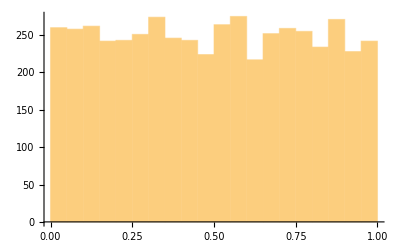

```mathematica
Histogram[Table[prg1[], {5000}]]
```

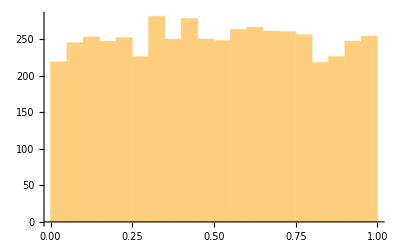

```mathematica
Histogram[Table[prg2[], {5000}]]
```

3) Реализуйте статистическую проверку  на основе критерия χ^2 для того, что выдаваемые значения распределены равномерно.

нужно реализовать функцию testChi2[list, m, p]. Эта функция принимает список l значений, которые выдал генератор и два параметра: число бинов m, и уровень достоверности 0 ≤ p ≤ 1. Функция будет возвращать True или False в зависимости от того, проходит тест или нет.

разбиваем отрезок [0,1] на m одинаковых бинов, находим y_k - количество значений из списка list, попавших k-ый бин.

вычисляем отклонения от ожидаемых значений y_k-n p_k, где n - это длина списка l, p_k=1/m - вероятность попадания в k-ый бин при равномерном распределении.

cчитаем значение статистики X=∑_(k=1)^m (y_k-n p_k)^2/(n p_k), оно должно подчиняться χ^2-распределению

сравниваем полученное значение X с процентными точками χ^2-распределения с ν=m-1 степенями свободы, которые можно получить с помощью обратной функции распределения InverseCDF. Например, для ν=9  (m=10) и уровня достоверности p=0.95 должно выполняться неравенство X<16.92 (значение 16.92 нужно получить с помощью InverseCDF).

если полученное нами значение X удовлетворяет неравенству, то мы считаем, что все хорошо, а если неравенство не соблюдается, то есть повод засомневаться. В примере со значениями из предыдущего пункта (m = 10, p = 0.95) для случайных величин с равномерным распределением лишь в p=5% случаев X превышал бы значение 16.92

```mathematica
testChi2[list_,m_,p_]:= Module[ {binnums,deviation, len, chival},len = Length[list];binnums = BinCounts[list, {0, 1, 1/m}];deviation = Map[ (# - len/m)&, binnums];chival = Map[#^2/(len/m)&, deviation];
chival =(Plus @@chival)//N;
pp = InverseCDF[ChiSquareDistribution[m-1],p];

chival < pp
]
```

```mathematica
testChi2[Table[prg1[],{5000}], 20, .95]
```

True

4) Проверьте ваши генераторы с помощью testChi2. (на самом деле, конечно, в Wolfram Mathematica реализованы очень многие функции для статистического анализа и проверки гипотез: Descriptive Statistics, Hypothesis Tests...)

```mathematica
Plus @@ Table[ testChi2[Table[prg1[],{100}], 20, .95], {5000}]
```

247 False+4753 True

```mathematica
Plus @@ Table[ testChi2[Table[prg2[],{100}], 20, .95], {5000}]
```

260 False+4740 True

5) А теперь сгруппируйте вывод генераторов в виде последовательных троек чисел {{α_0,α_1,α_2}, {α_3,α_4,α_5}, ...}. Постройте эти точки в трехмерном пространстве. Что мы ожидаем для случайных величин? Можно ли назвать случайными точки, получаемыми вторым генератором?

```mathematica
ListPointPlot3D[Table[Table[prg1[], {3}], {5000}]]
```

-Graphics3D-

Точки случайные

```mathematica
ListPointPlot3D[Table[Table[prg2[], {3}], {5000}]]
```

-Graphics3D-

Точки не случайные

## Одномерное случайное блуждание

В начальный момент времени частица находится в точке 0. На каждом следующем шаге она перемещается на 1 в положительном или отрицательном направлении с вероятностью 1/2.  Далее нас будут интересовать некоторые свойства траектории этой частицы в зависимости от числа шагов.

Напишите функцию path[nSteps], которая порождает некоторую траекторию случайного движения длиной nSteps шагов. Воспользуйтесь хорошим генератором случайных чисел из предыдущего задания. Для порождения списка может быть полезна функция NestList[]

```mathematica
path[nSteps_]:=Module[{},f[x_] :=  Sign[prg1[]-1/2] + x;NestList[f, 0, nSteps]];
path[5]
```

{0,-1,0,1,0,-1}

{0,1,0,-1,-2,-1}

Исследуйте некоторые статистические закономерности в поведении траекторий. Напишете функцию distAverage[nSteps, nPaths], которая вычисляет бы среднее по nPaths траекториям расстояние, на которое уходит частица за nSteps шагов. Постройте график distAverage в зависимости от числа шагов nSteps.

```mathematica
distAverage[nSteps_, nPaths_]:= Mean[ Table[ path[nSteps]//Last //Abs, {nPaths}] ];
steps =Table[distAverage[nst, 200] , {nst,1,100}];
fit = Fit[steps, Sqrt[x], x]
```

0.792213 √x

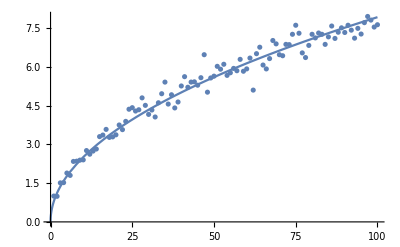

```mathematica
Show[ ListPlot[steps], Plot[fit, {x,0, 100}]]
```

```mathematica
Print[2/Pi//Sqrt // N]
```

0.797885

Значения среднего расстояния distAverage аппроксимируйте функцией вида d̄=α √n_steps, убедитесь, что α близко к √(2/π).

Напишите функцию distribution[nSteps, nPaths], которая возвращала бы все возможные положения частицы в конце пути длиной nSteps шагов вместе с оценкой для их вероятности, полученной по nPaths траекториям. Например,

```mathematica
distribution[nSteps_, nPaths_]:=MapAt[#/nPaths&, Tally[ Table[path[nSteps]//Last, {nPaths}]], {All,2}]
distribution[2,10]
```

{{0,3/5},{-2,1/5},{2,1/5}}

```mathematica
(* из 10 случайных траекторий длиной в 2 шага,
две закончились в точке -2, пять в точке 0,  три в точке +2 *)
```

{{-2,0.2},{0,0.5},{2,0.3}}

Напишите функцию distributionExact[nSteps], которая возвращала бы точное значение вероятностей каждого из конечных положений частицы на траектории длиной nSteps шагов.

Для этого рассмотрите значения степеней x и коэффициенты перед ними в последовательности:

((x+x^-1)/2)^0=x^0, 
((x+x^-1)/2)^1=x^1/2+x^-1/2
((x+x^-1)/2)^2=x^2/4+x^0/2+x^-2/4

…

((x+x^-1)/2)^n=x^n/2^n+...+x^-n/2^n

Можно заметить следующее: умножение на (1/2 x+1/2 x^-1) можно интерпретировать как увеличение степени x на 1 с вероятностью 1/2 либо уменьшение степени x на 1 с той же вероятностью 1/2

```mathematica
distributionExact[nSteps_]:= Table[ {k-(nSteps-k), Binomial[nSteps,k]/Power[2,nSteps]}, {k, 0, nSteps}]
distributionExact[5]
```

{{-5,1/32},{-3,5/32},{-1,5/16},{1,5/16},{3,5/32},{5,1/32}}

Сравните экспериментальные значения для распределения конечных положений частицы (для досточно большого числа nPaths)  с точными значениями

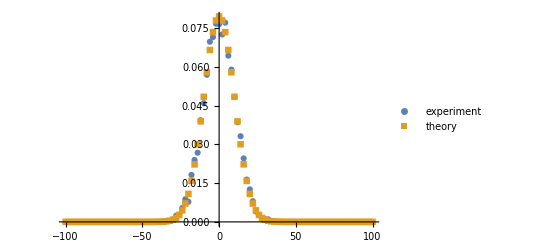

```mathematica
ListPlot[{ distribution[100, 5000], distributionExact[100]}, PlotMarkers->Automatic, PlotLegends->{"experiment", "theory"}]
```

Получите значение среднего расстояния, на которое уходит частица за n-шагов, через точное распределение вероятностей положений после n-шагов и попробуйте аналитически получить формулу с помощью Mathematica d̄≈√(2/π)√n, n→∞.

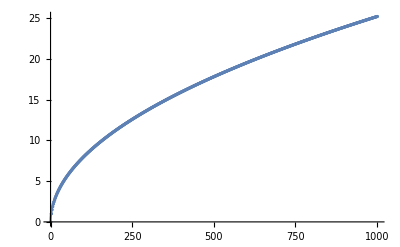

```mathematica
meanDistance[nSteps_] := Map[Abs[Times@@#]&, distributionExact[nSteps]] //Total
Show[ ListPlot[Table[meanDistance[i], {i, 0, 1000}]], Plot[ Sqrt[2x/Pi], {x,0,1000}]]
```